# Curve Tracing

Let

```mathematica
f[x_]:=(x^2-1)*Tan[x]
```

be a function defined on[-π/2,π/2]. We want to find its roots, extreme values i.e. minima, maxima, and saddle points, inflection points, and if applicable, singularities and limits.

## Plot

The plot for the function f is the following.

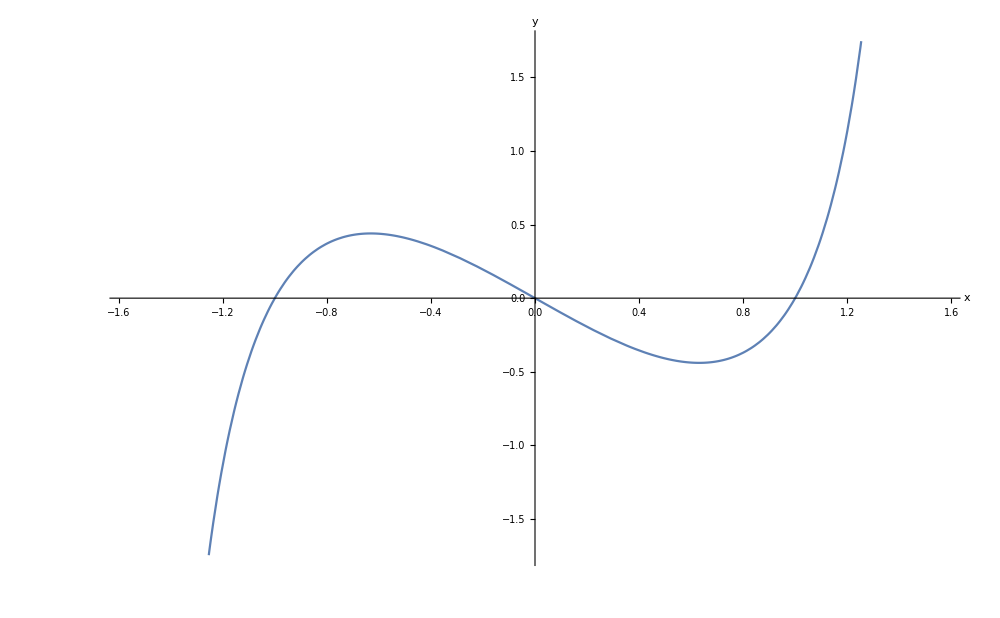

```mathematica
Plot[(x^2-1)*Tan[x],{x,-π/2,π/2},ImageSize->1000,AxesLabel->{x,y}]
```

## Roots

Mathematica will find the roots for us numerically.

```mathematica
FindRoot[f[x],{x,-1}]
```

{x→-1.}

```mathematica
FindRoot[f[x],{x,0}]
```

{x→0.}

```mathematica
FindRoot[f[x],{x,1}]
```

{x→1.}

Therefore, the function f has three roots (intersections with the x axis). These are (-1, 0); (0, 0); and (1, 0).

```mathematica
Simplify[f[x]=0]
```

0

Setting the function f to zero, we get the intersection with the y axis which is at (0, 0).

## Extreme Values

In this section, we want to find all maxima, minima and saddle points of the function f.

## Derivatives

Before we consider the extreme values for the function f, we want to find its derivatives. We have

```mathematica
f'[x]
```

```mathematica
(-1+x^2) Sec[x]^2+2 x Tan[x]
```

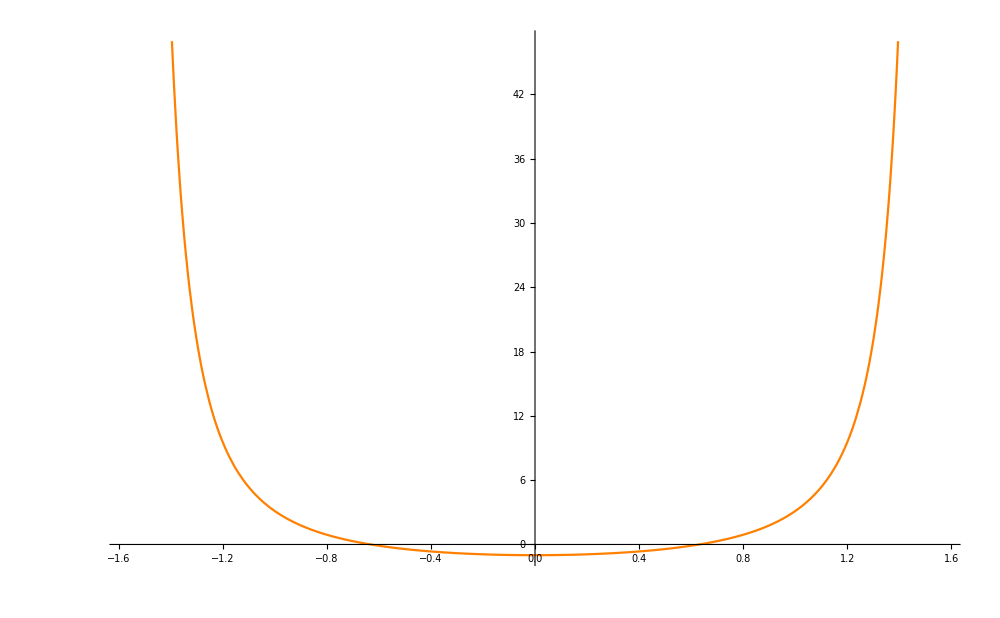

```mathematica
Plot[f'[x],{x,-π/2,π/2},PlotStyle->Orange, ImageSize->1000AxesLabel->{x,y}]
```

```mathematica
f''[x]
```

4 x Sec[x]^2+2 Tan[x]+2 (-1+x^2) Sec[x]^2 Tan[x]

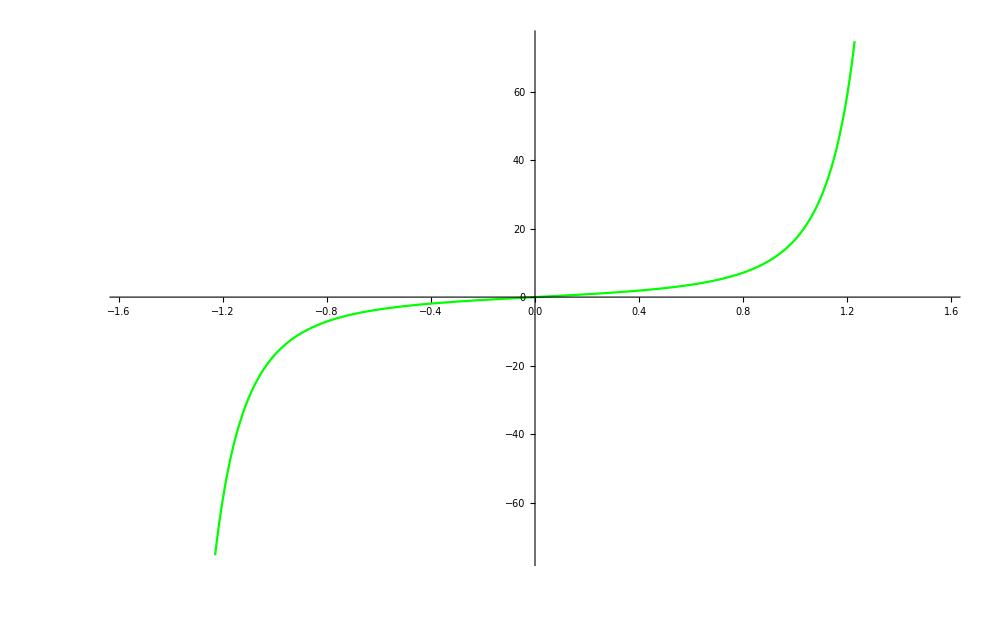

```mathematica
Plot[f''[x],{x,-π/2,π/2}, ImageSize->1000,PlotStyle->Green]
```

Putting the original function and its two derivatives in a plot, we get

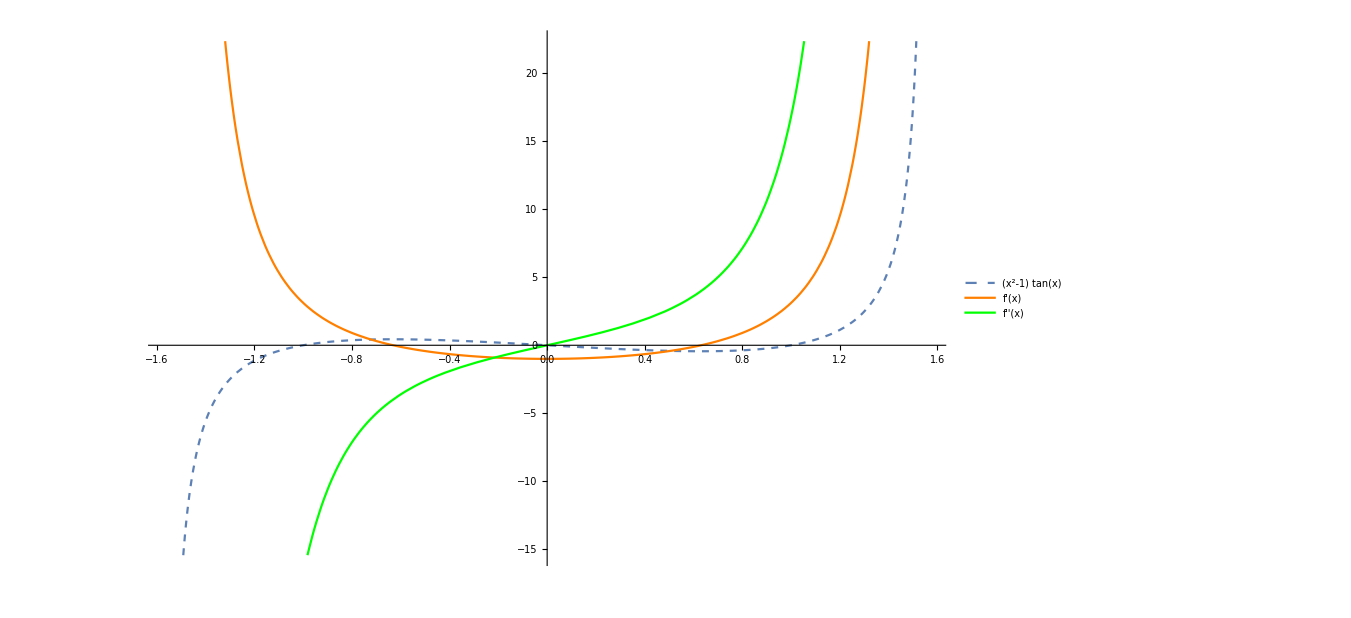

```mathematica
Plot[{(x^2-1)Tan[x],f'[x],f''[x]},{x,-π/2,π/2}, ImageSize->1000,PlotStyle-> {Dashed, Orange, Green},PlotLegends->"Expressions"]
```

## Extreme Values

For the extreme values we have

```mathematica
FindMinimum[(x^2-1)Tan[x],{x,0.5}]
```

{-0.439732,{x→0.631264}}

```mathematica
FindMaximum[(x^2-1)Tan[x],{x,-0.5}]
```

{0.439732,{x→-0.631264}}

To find saddle points we have

```mathematica
FindRoot[f'[x],{x,-1}]
```

{x→-0.631264}

```mathematica
FindRoot[f'[x],{x,1}]
```

{x→0.631264}

These extreme values are already a minimum or a maximum; therefore, the function f does not have any saddle points.

## Inflection Points

To find inflection points, we compute

```mathematica
FindRoot[f''[x],{x,0}]
```

{x→0.}

```mathematica
f''[0]
```

0

Therefore, the function f does not have any inflection points.

## Singularity

The function f does not have a singularity in [-π/2,π/2]  since tan(x) = (sin(x))/(cos(x)), but cos(x) is never 0 for the given domain. In other words, the function f is defined everywhere on the given domain.

## Limits

Since we do not have any singularity and the domain is a closed set, there is no limit to sensibly evaluate.